Your Title Here

```mathematica
Manipulate[
Module[{w,h,θ,RA,RB,FA,FB,Fx},
w=6;h=5;θ=ArcTan[h/(w/2)];

RB=B/.N@Quiet@Solve[0==w/2*(-F)+w*B,B][[1]];
RA=A/.N@Quiet@Solve[0==A+RB-F,A][[1]];

FA=Module[{s1},
s1=N@√((w/2)^2+h^2);
f/.Quiet@Solve[s1/h==f/RA,f][[1]]];

FB=Module[{,s1},
s1=B/.Quiet@Solve[0==-F+FA*Sin[θ]+B,B][[1]];
f/.Quiet@Solve[Sin[θ]==s1/f,f][[1]]];

Fx=Module[{s1},
s1=N@√((w/2)^2+h^2);
f/.Quiet@Solve[(w/2)/s1==-f/FB,f][[1]]];

Graphics[{
{Thickness@0.025,GrayLevel@0.5,Line[{{w/2,h},{w,h},{w,0}}]},
{Arrowheads@0.07,
Thickness[0.025*Rescale[-Fx,{0.3,3}]],Red,Arrow[{{0,0},{w/2,0}}],Arrow[{{w,0},{w/2,0}}],
Thickness[0.025*Rescale[RA,{0,5.8}]],RGBColor[0,0.6,0],Arrowheads@{-0.07,0.07},Arrow[{{0,0},{w/2,h}}],Arrow[{{w/2,h},{w,0}}]},
{PointSize@0.035,Point@{{0,0},{w,0},{w/2,h},{w,h}}},
{Arrowheads@0.07,{Blue,
{Thickness[0.02*Rescale[F,{0,10}]],Arrow[{{w/2,1.5*h},{w/2,h}}]},Text[Style[Row@{NumberForm[F,{3,1}]," kN"},17],{w/2,1.5*h},{0,-1}],
{Thickness[0.02*Rescale[#1,{0,10}]],Arrow[{{#2,-0.5*h},{#2,0}}],Text[Style[Row@{NumberForm[#1,{4,1}]" kN"},17],{#2,-0.5*h},{0,1}]}&@@@{{RA,0},{RB,w}}},
Text[Style[Column[{Row@{NumberForm[#1,{3,1}]," kN"},"compression"},Center],18,RGBColor[0,0.6,0],Background->White],{#2,h/2}]&@@@{{FA,w/4},{FB,w/2+w/4}},
Text[Style[Column[{Row@{NumberForm[Fx,{3,1}]," kN"},"tension"},Center],18,Red,Background->White],{w/2,0},{0,-1.5}],
Text[Style["0 kN",18,Background->White],{w,h/2}],Text[Style["0 kN",18,Background->White],{w/2+w/4,h}]
}
},ImageSize->{600,430},AspectRatio->Full,PlotRangePadding->Scaled@0.03]
],
Control[{{F,5,"downward force"},1,10,0.1,Appearance->"Labeled"}]
]
```

Null::shdw: Symbol Null appears in multiple contexts {Notebook$$18$415320`,System`}; definitions in context Notebook$$18$415320` may shadow or be shadowed by other definitions.

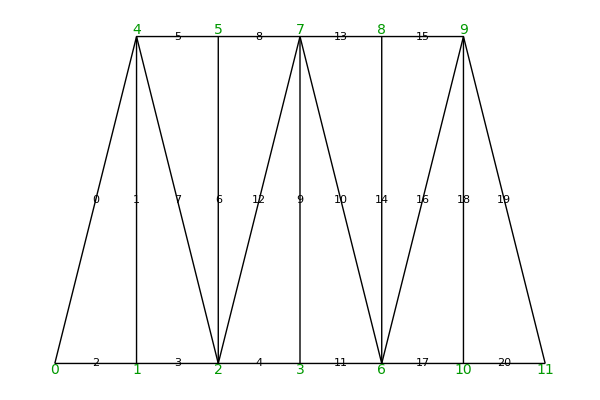

```mathematica
Module[{w,h,θ},
w=5;h=5;θ=ArcTan[h/(w/2)];

Graphics[{
Thick,
Line[{{#*w,0},{#*w+w,h},{#*w+2*w,0}}]&/@Range[0,5,2],
Line[{{w,h},{5*w,h}}],Line[{{0,0},{6*w,0}}],Line[{{#*w,0},{#*w,h}}]&/@Range@5,

Text[Framed[Style[Row@{" ",#1," "},14,Blue],Background->White,FrameMargins->Small,RoundingRadius->10],#2]&@@@{{0,{w/2,h/2}},{1,{w,h/2}},{2,{w/2,0}},{3,{1.5*w,0}},{4,{2.5*w,0}},{5,{1.5*w,h}},{6,{2*w,h/2}},{7,{1.5*w,h/2}},{8,{2.5*w,h}},{9,{3*w,h/2}},{10,{3.5*w,h/2}},{11,{3.5*w,0}},{12,{2.5*w,h/2}},{13,{3.5*w,h}},{14,{4*w,h/2}},{15,{4.5*w,h}},{16,{4.5*w,h/2}},{17,{4.5*w,0}},{18,{5*w,h/2}},{19,{5.5*w,h/2}},{20,{5.5*w,0}}},

Text[Style[#1,14,RGBColor[0,0.6,0],Background->White],#2,{0,1.5}]&@@@{{0,{0,0}},{1,{w,0}},{2,{2*w,0}},{3,{3*w,0}},{6,{4*w,0}},{10,{5*w,0}},{11,{6*w,0}}},
Text[Style[#1,14,RGBColor[0,0.6,0],Background->White],#2,{0,-1.5}]&@@@{{4,{w,h}},{5,{2*w,h}},{7,{3*w,h}},{8,{4*w,h}},{9,{5*w,h}}}
},ImageSize->{600,400}]
]
```

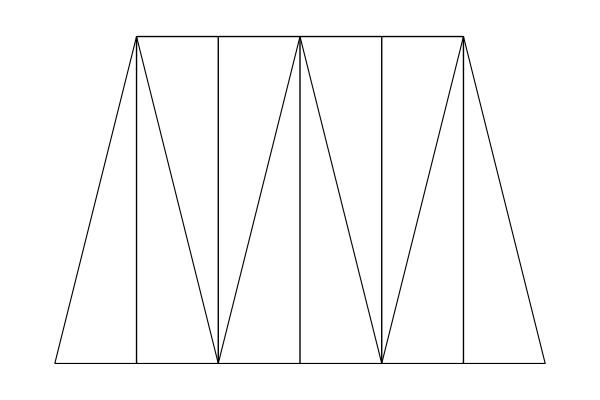





```mathematica
Module[{w,h,θ},
w=5;h=5;θ=ArcTan[h/(w/2)];

Graphics[{
{EdgeForm@Thick,FaceForm@None,Polygon[{{#*w,0},{#*w+w,h},{#*w+2*w,0}}]&/@Range[0,5,2]},
{Thick,Line[{{w,h},{5*w,h}}],Line[{{#*w,0},{#*w,h}}]&/@Range@5}
},ImageSize->{600,400}]
]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX